# Chemotactic walk of Lablet in chemical field at steady state

### Abhishek Sharma Ruhr Universität, Bochum Germany

## Description

In this Mathematica notebook, we consider dynamics of self propelled particle (Lablet) in the chemical field. This formulation was taken from two references, 

1) Johannes Taktikos, Vasily Zaburdaev, and Holger Stark, Modeling a self-propelled autochemotactic walker, Phys. Rev. E 84, 041924 

2) Johannes Taktikos, Vasily Zaburdaev, and Holger Stark, Collective dynamics of model microorganisms with chemotactic signaling,  Phys. Rev. E 85, 051901

## Chemotaxis with constant speed in constant field

We assume Lablet moves with constant speed, hence in two dimensions, velocity at any general time is given by  V(t)=v e(t). 

We assume chemotatic field is given by, E. So, we could define the driving potential as 
V(e)= -e.E.

Based on this, we can write governing equation of the motion of the particle for rotational and kinematic motion as,

ⅆ/ⅆt L=-γ_RΩ + M_ext+Τ(t)

ⅆ/ⅆt e=Ω ×e

Using these equations, in the overdamped limit (neglecting inertial effects), we can write

ⅆ/ⅆt e=1/γ_R(ℐ-e⊗e)E+1/γ_R Τ(t)×e

Substituting in this equation,  e=(cosϕ, sinϕ, 0)^T, E=(E_x,E_y,0)^T, Τ(t)=(0,0,Τ(t))^T, the equation simplifies to,

ⅆ/ⅆt ϕ(t)=-E_x/γ_Rsinϕ(t)+E_y/γ_R cosϕ(t)+√(2 q_ϕ)Τ(t)

#### Constant chemotactic field along X direction

In the absense of noise and constant chemotact field along x direction, 

ⅆ/ⅆt ϕ(t)=-E_x/γ_Rsinϕ(t)

```mathematica
eq = D[ϕ[t],t]== -Ex/γR Sin[ϕ[t]];
```

```mathematica
ic=ϕ[0]==ϕ0;
```

```mathematica
sol=DSolve[{eq,ic},ϕ[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ϕ[t]→2 ArcCot[ⅇ^((Ex t)/γR) Cot[ϕ0/2]]}}

Hence, the trajectory of the particle is given by, 

ⅆ/ⅆt r(t)=v e(t)

```mathematica
solX=DSolve[{D[x[t],t]== v Cos[ϕ[t]]/.First[sol],x[0]== 0},x[t],t]
```

{{x[t]→-1/Ex v (Ex t+γR Log[2]-γR Log[1+ⅇ^((2 Ex t)/γR)-Cos[ϕ0]+ⅇ^((2 Ex t)/γR) Cos[ϕ0]])}}

```mathematica
solY=DSolve[{D[y[t],t]== v Sin[ϕ[t]]/.First[sol],y[0]== 0},y[t],t]
```

{{y[t]→-1/Ex 2 (v γR ArcTan[Cot[ϕ0/2]]-v γR ArcTan[ⅇ^((Ex t)/γR) Cot[ϕ0/2]])}}

```mathematica
params={Ex-> 1.,γR-> 2.,v-> 1.0};
```

```mathematica
f[ϕ0_]=Evaluate[{x[t]/.First[solX],y[t]/.First[solY]}/.params]
```

{-1. (1.38629+1. t-2. Log[1+ⅇ^(1. t)-Cos[ϕ0]+ⅇ^(1. t) Cos[ϕ0]]),-2. (2. ArcTan[Cot[ϕ0/2]]-2. ArcTan[ⅇ^(0.5 t) Cot[ϕ0/2]])}

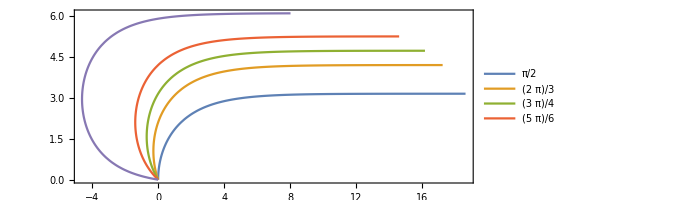

```mathematica
ParametricPlot[Evaluate[f[#]&/@{π/2,(2π)/3,(3π)/4,(5π)/6,π-0.1}],{t,0,20},Frame-> True,PlotLegends-> {π/2,(2π)/3,(3π)/4,(5π)/6}]
```

## Case 2: Two dimensional field from coplanar electrodes (using conformal mapping)

#### Conformal map to coplanar geometry from parallel plate geometry

```mathematica
Clear[t,t1,t2,t3,t4]
```

```mathematica
(* Changing from the T Space to U Space *)
f0[t_]=∫(C/(√((t-t1)(t-t2)(t-t3)(t-t4))))ⅆt;
```

```mathematica
FullSimplify[f0[t]]
(* Simplifying this gives the following Form,  the constant C is calculated from the complete Integral, F(t3) = 1 *)
```

(2 C (t-t2) √(((-t1+t2) (t-t3))/((t-t1) (t2-t3))) (t-t4) EllipticF[ArcSin[√(((t-t2) (t1-t4))/((t-t1) (t2-t4)))],((t1-t3) (t2-t4))/((t2-t3) (t1-t4))])/(√((t-t1) (t-t2) (t-t3) (t-t4)) √(((t-t2) (-t1+t2) (t-t4) (t1-t4))/((t-t1)^2 (t2-t4)^2)) (t2-t4))

```mathematica
f[t_]= (2C)/(√((t2-t3)(t1-t4))) EllipticF[ArcSin[√(((t-t2) (t1-t4))/((t-t1) (t2-t4)))],((t1-t3) (t2-t4))/((t2-t3) (t1-t4))];
f1[t_] =  EllipticF[ArcSin[√(((t-t2) (t1-t4))/((t-t1) (t2-t4)))],((t1-t3) (t2-t4))/((t2-t3) (t1-t4))];
```

```mathematica
aa=Chop[EllipticF[ArcSin[√(((t3-t2) (t1-t4))/((t3-t1) (t2-t4)))],((t1-t3) (t2-t4))/((t2-t3) (t1-t4))]];
```

```mathematica
g[t_] := ArcSin[√(((t-t2) (t1-t4))/((t-t1) (t2-t4)))];
 p = ((t1-t3) (t2-t4))/((t2-t3) (t1-t4));
(* Complete Elliptical Integral*)
iK = EllipticK[p];
t1=-2;t2=-0.4;t3=0.4;t4=2; (* Assumed *)
FF[t_] = f1[t]/aa;
```

```mathematica
p1=ParametricPlot[With[{ω=u+I v},{Re[ω],Im[ω]}],{u,0,1},{v,0,1}, Mesh-> Full,MeshStyle-> {Red}];
```

```mathematica
p2=ParametricPlot[With[{ω=u+I v,b= FF[u+I v] },{Re[b],Im[b]}],{u,-1,1},{v,0,1}, Mesh-> Full,MeshStyle-> {Red},PlotRange-> {0.,0.9}];
```

```mathematica
(* Trying to make the Invert Plots for the same *)
```

```mathematica
FK[u_,v_] = Flatten[Solve[f1[t]== aa (u+I v),t]]⟦1,2⟧;
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
p3=ParametricPlot[With[{ω=u+I v,b= FK[u,v] },{Re[b],Im[b]}],{u,0,1},{v,0,0.95},MeshStyle->{Red},Mesh-> {20,20},AspectRatio->0.6];
```

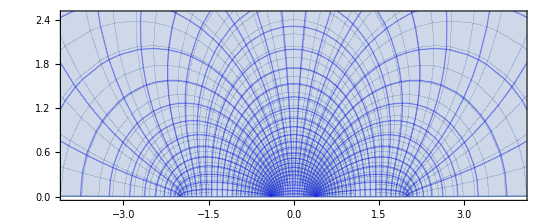

```mathematica
ParametricPlot[With[{ω=u+I v,b= FK[u,v]},{Re[b],Im[b]}],{u,0,1},{v,0,0.95},Mesh-> {30,30},MeshStyle-> Blue]
```

Here, we will use one dimensional conformally invariant steady state solution for fast chemical reaction at the electrode. Conformal invariance could be found in Bazant et al, 2004.

```mathematica
V =10.;
J = Tan[V/4.];
Conc[ω_]:= 1 +J Re[ω];
K=0.1;
Pot[ω_] := Log[(1 + J Re[ω])/(K(1-J^2))];
```

```mathematica
intp1=Interpolation[Flatten[Table[{{Re[Sin[FK[u,v]]],Im[Sin[FK[u,v]]]},Conc[u+I v]},{u,0,1,0.01},{v,0,0.8,0.01}],1]]
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

InterpolatingFunction[{{-18.8294, 18.8294}, {-3.46337, 28.1211}}, <>]

#### Solution for coplanar geometry

```mathematica
p1=ListContourPlot[Flatten[Table[{Re[Sin[FK[u,v]]],Im[Sin[FK[u,v]]],Conc[u + I v] },{u,0,1,0.01},{v,0,0.8,0.01}],1],Contours->20,ContourLabels-> All,ColorFunction->"DarkRainbow",PlotLabel-> "Concentration distribution at steady state",PlotRange->{{-5,5},{0,5},All}];
```

```mathematica
p2=ListContourPlot[Flatten[Table[{Re[Sin[FK[u,v]]],Im[Sin[FK[u,v]]],Pot[u + I v] },{u,0,1,0.01},{v,0,0.8,0.01}],1],Contours->20,ContourLabels-> All,ColorFunction->"DarkRainbow",PlotLabel-> "Potential distribution at steady state",PlotRange->{{-5,5},{0,5},All}];
```

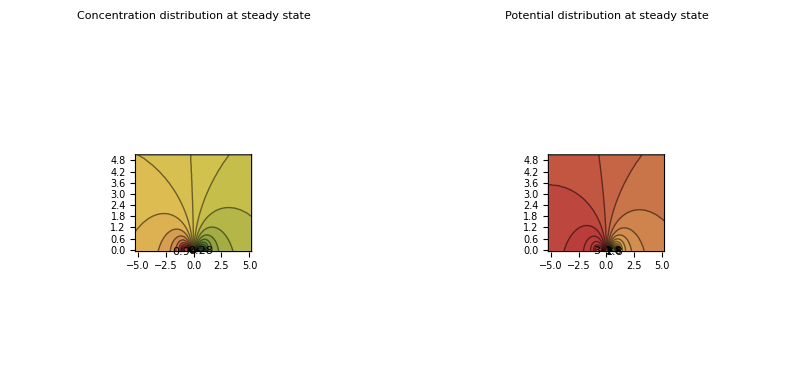

```mathematica
GraphicsRow[{p1,p2},Frame-> All]
```

```mathematica
intp1=Interpolation[Flatten[Table[{{Re[Sin[FK[u,v]]],Im[Sin[FK[u,v]]]},Conc[u+I v]},{u,0,1,0.01},{v,0,0.8,0.01}],1]]
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

InterpolatingFunction[{{-18.8294, 18.8294}, {-3.46337, 28.1211}}, <>]

```mathematica
intp2=Interpolation[Flatten[Table[{{Re[Sin[FK[u,v]]],Im[Sin[FK[u,v]]]},Pot[u+I v]},{u,0,1,0.01},{v,0,0.8,0.01}],1]]
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

InterpolatingFunction[{{-18.8294, 18.8294}, {-3.46337, 28.1211}}, <>]

```mathematica
GraphicsRow[{DensityPlot[intp1[i,j],{i,-5,5},{j,0,5},PlotRange-> All,PlotLabel-> "Concentration distribution",ColorFunction->"SunsetColors",PlotLegends->Automatic],DensityPlot[intp2[i,j],{i,-5,5},{j,0,5},PlotRange-> All,PlotLabel-> "Potential distribution",ColorFunction->"SunsetColors",PlotLegends->Automatic]},Frame-> All]
```

-Graphics-

```mathematica
dInpt1X[X_?NumericQ,Y_?NumericQ]=D[intp1[X,Y],X]
```

InterpolatingFunction[{{-18.8294, 18.8294}, {-3.46337, 28.1211}}, <>][X,Y]

```mathematica
dInpt1Y[X_?NumericQ,Y_?NumericQ]=D[intp1[X,Y],Y]
```

InterpolatingFunction[{{-18.8294, 18.8294}, {-3.46337, 28.1211}}, <>][X,Y]

```mathematica
dInpt1X2[X_?NumericQ,Y_?NumericQ]=D[D[intp1[X,Y],X],X]
```

InterpolatingFunction[{{-18.8294, 18.8294}, {-3.46337, 28.1211}}, <>][X,Y]

```mathematica
dInpt1Y2[X_?NumericQ,Y_?NumericQ]=D[D[intp1[X,Y],Y],Y]
```

InterpolatingFunction[{{-18.8294, 18.8294}, {-3.46337, 28.1211}}, <>][X,Y]

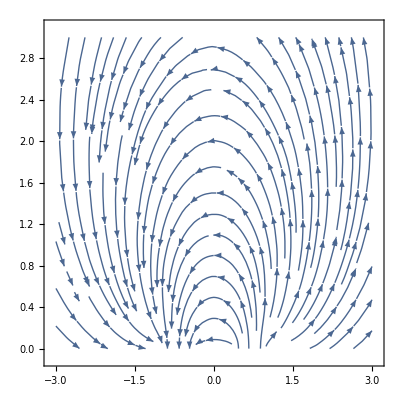

```mathematica
StreamPlot[{dInpt1X[X,Y],dInpt1Y[X,Y]},{X,-3,3},{Y,0,3}]
```

```mathematica
Clear[eq,eq1,eq2]
```

```mathematica
eq1 = D[ϕ[t],t]== -dInpt1X[pX[t],pY[t]]/γR Sin[ϕ[t]]+dInpt1Y[pX[t],pY[t]]/γR Cos[ϕ[t]];
```

```mathematica
eq2=D[pX[t],t]==v Cos[ϕ[t]];
```

```mathematica
eq3=D[pY[t],t]==v Sin[ϕ[t]];
```

```mathematica
ic1=ϕ[0]==ϕ0;
```

```mathematica
ic2=pX[0]==pX0;
```

```mathematica
ic3=pY[0]==pY0;
```

```mathematica
params={γR-> 0.2,v->0.005,pX0->2.0,pY0-> 2.0,ϕ0->π/3};
```

```mathematica
solN=NDSolve[Evaluate[{eq1,eq2,eq3,ic1,ic2,ic3}/.params],{pX[t],pY[t],ϕ[t]},{t,0,1550}]
```

{{pX[t]→InterpolatingFunction[{{0., 1550.}}, <>][t],pY[t]→InterpolatingFunction[{{0., 1550.}}, <>][t],ϕ[t]→InterpolatingFunction[{{0., 1550.}}, <>][t]}}

```mathematica
{pX[0],pY[0]}/.solN
```

{{pX[0],pY[0]}}

```mathematica
px1=ParametricPlot[{pX[t],pY[t]}/.solN,{t,0,1550},Frame-> True,PlotRange->{{-5,5},{-5,10}},PlotStyle-> Dotted];
```

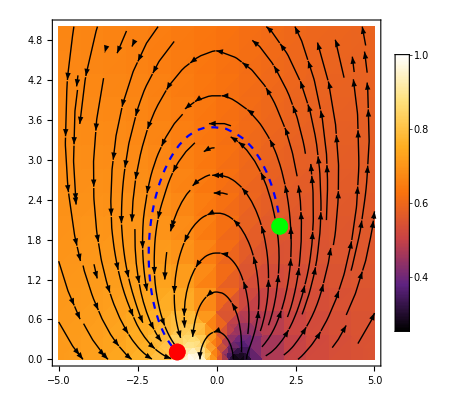

```mathematica
Show[DensityPlot[intp1[i,j],{i,-5,5},{j,0,5},PlotRange-> All,ColorFunction->"SunsetColors",PlotLegends->Automatic],ParametricPlot[{pX[t],pY[t]}/.solN,{t,0,1550},Frame-> True,PlotRange->{{-5,5},{-5,10}},PlotStyle-> {Blue,Dashed,Thick}],StreamPlot[{dInpt1X[X,Y],dInpt1Y[X,Y]},{X,-5,5},{Y,0,5},StreamPoints-> 50,StreamStyle-> Black],ListPlot[({pX[t],pY[t]}/.solN)/.t-> 0, PlotStyle-> {Green,PointSize[0.03]}],ListPlot[({pX[t],pY[t]}/.solN)/.t-> 1550, PlotStyle-> {Red,PointSize[0.03]}]]
```